```mathematica
(* Simplex Algorithm Written by Kyle Salitrik *)
$Line=0;
RemoveGlobal[]:=(ClearGlobal[];Remove["Global`*"];);
RemoveGlobal[];
```

```mathematica
(* Check for Bad Row *)
checkBadRow[m_,i_]:=(
(* Get ith row *)
iRow=m[[i]];
cols=Dimensions[iRow][[1]];
If[AllTrue[Part[iRow,1;;cols-1],#≤0&],
Return[True],
Return[False]
];
)
```

```mathematica
(* Check for Bad Column *)
checkBadColumn[m_]:=(
(* Get row and column counts *)
rows=Dimensions[m][[1]];
cols=Dimensions[m][[2]];

(* Get jth Column *)
For[col = 1, col <cols-1,col++,
AllTrue[Part[m[[All,cols-1]],2;;rows-1],#≥0&];m
If[m[[rows,col]]<0 && AllTrue[Part[m[[All,col]],2;;rows-1],#≥0&],
Return[True]
];
];
Return[False]
)
```

```mathematica
(* Check B Feasible: Returns -1 if infeasible, 1 if Phase I, 2 if Phase II *)
checkFeasibility[m_]:=(
(* Get number of rows and cols *)
rows=Dimensions[m][[1]];
cols=Dimensions[m][[2]];
bCol =cols-1;

If[AllTrue[Part[m[[All,cols-1]],2;;rows-1],#≥0&], 
(* All B values are greater than or equal to 0 -> Continue to Phase II *)
Return[2]
];

(* Check B column for negatives and return condition of current tableaux *)
For[row = 2, row<rows,row++,
If[m[[row,bCol]]<0,
If[checkBadRow[m,row]==True,
Return[-1];
]
]
];

(* No bad rows were found but some values are less than 0, continue Phase I *)
Return[1]
)
```

```mathematica
(* Check if Tableaux is Optimal given that it is feasible *)
checkOptimality[m_]:=(
(* Get number of rows and cols *)
rows=Dimensions[m][[1]];
cols=Dimensions[m][[2]];

(* Check C vector *)
If[AllTrue[Part[m[[rows]],1;;cols-2],#≥0&],
Return[True],
Return[False]
];
)
```

```mathematica
(* Finds row position of first bi less than 0 and returns the value *)
getFirstNegativeB[m_]:=(
(* Get number of rows and cols *)
rows=Dimensions[m][[1]];
cols=Dimensions[m][[2]];

(* Finds and returns the first negative value in the B vector. This position is incremented by 1 because
slicing the vector out of the matrix removes the first row *)
Return[Flatten[FirstPosition[Part[m[[All,cols-1]],2;;rows-1], x_/; x<0]][[1]] + 1]
)
```

```mathematica
(* Blands rule: Returns the correct variable to use based on blands rule if ties occur during the Simplex Algorithm *)
blandsRule[potentialSolutions_, blandVector_]:=(
blandPositions = Flatten[Position[blandVector,Alternatives@@potentialSolutions]];
Return[Extract[blandVector,Min[blandPositions]]];
)
```

```mathematica
(* Finds jStar according to the rules for Phase I *)
getJStarP1[m_,iStar_]:=(
(* Get number of columns *)
cols=Dimensions[m][[2]];

(* Get list of positions where a_[i0,j] > 0 *)
Return[Extract[m[[1]],Position[Part[m[[iStar]],1;;cols-1],x_/;x>0]]];
)
```

```mathematica
(* Finds jStar according to the rules for Phase II *)
getJStarP2[m_,iStar_]:=(
(* Get number of columns *)
cols=Dimensions[m][[2]];

(* Get list of positions where a_[i0,j] > 0 *)
Return[Extract[m[[1]],Position[Part[m[[iStar]],1;;cols-2],x_/;x<0]]];
)
```

```mathematica
(* Max Test Function: Returns the index of the max value. *)
maxTest[m_,jStar_,i0_,basicVars_,verbose_]:=(
(* Get jth column *)
rows=Dimensions[m][[1]];

(* Create temporary array to get max position from *)
compArray={$MaxNumber};

(* Get negative column values and divide by corresponding b_i value*)
For[row=2, row≤i0, row++,
If[(m[[row,jStar]] < 0 || row==i0) && m[[row,cols-1]]≠ 0,
AppendTo[compArray,m[[row,jStar]]/m[[row,cols-1]]],
AppendTo[compArray,$MaxNumber]
]
];

minPositions=Position[compArray,Min[compArray]];

If[verbose,
Print["Max Comparison Array: ",compArray,
	"\nMax Position: ", minPositions,
	"\nExtraction: ", Extract[basicVars,minPositions]];
];

Return [Flatten[Extract[basicVars,minPositions]]];
)
```

```mathematica
(* Finds and returns the list {iStar, jStar} according to rules for Phase I *)
findStarsP1[m_,i0_,blandVector_,verbose_]:=(
basicVars = m[[All,Dimensions[m][[2]];;]];
nonBasicVars=m[[1]];
jStar=Null;

(* Find candidates for jStar *)
jStarCandidates = getJStarP1[m,i0];

(* If multiple candidates are found, determine jStar using Bland's rule *)
If[Length[jStarCandidates] > 1,
jStarBlandResult=blandsRule[jStarCandidates,blandVector];
jStar=Flatten[Position[nonBasicVars,jStarBlandResult]][[1]];,
jStar=Flatten[Position[nonBasicVars,jStarCandidates[[1]]]][[1]];
];

(* Find iStar *)
iStar = Null;
iStarCandidates=maxTest[m,jStar,i0,basicVars,verbose];

(* If multiple candidates are found, determine iStar using Bland's rule *)
If[Length[iStarCandidates] > 1,
iStarBlandResult=blandsRule[iStarCandidates,blandVector];
iStar=Flatten[Position[basicVars,iStarBlandResult]][[1]];,
iStar=Flatten[Position[basicVars,Flatten[iStarCandidates]]][[1]];
];


(* Check if iStar is past i0 or no better iStar was found *)
If[(iStar == Null ||iStar>i0),
iStar=i0;
];

If[verbose,
Print[
	"basicVars: ", basicVars,
	"\nNon-Basic Vars: ", nonBasicVars,
	"\njStar Candidates: ", jStarCandidates,
	"\njStar Bland's Rule Result: ", jStarBlandResult,
	"\njStar: ",jStar,
	"\niStar Candidates: ", iStarCandidates,
	"\niStar Bland's Rule Result: ", iStarBlandResult,
	"\niStar: ",iStar];
];

Return[{iStar,jStar}];
)
```

```mathematica
(* Finds and returns the list {iStar, jStar} according to rules for Phase II *)
findStarsP2[m_,i0_,blandVector_,verbose_]:=(
basicVars = m[[All,Dimensions[m][[2]];;]];
nonBasicVars=m[[1]];
jStar=Null;

(* Find candidates for jStar *)
jStarCandidates = getJStarP2[m,i0];

(* If multiple candidates are found, determine jStar using Bland's rule *)
If[Length[jStarCandidates] > 1,
jStarBlandResult=blandsRule[jStarCandidates,blandVector];
jStar=Flatten[Position[nonBasicVars,jStarBlandResult]][[1]];,
jStar=Flatten[Position[nonBasicVars,jStarCandidates[[1]]]][[1]];
];


(* Find iStar *)
iStar = Null;
iStarCandidates=maxTest[m,jStar,i0-1,basicVars,verbose];

(* If multiple candidates are found, determine iStar using Bland's rule *)
If[Length[iStarCandidates] > 1,
iStarBlandResult=blandsRule[iStarCandidates,blandVector];
iStar=Flatten[Position[basicVars,iStarBlandResult]][[1]];,
iStar=Flatten[Position[basicVars,Flatten[iStarCandidates]]][[1]];
];

If[verbose,
Print[
	"basicVars: ", basicVars,
	"\nNon-Basic Vars: ", nonBasicVars,
	"\njStar Candidates: ", jStarCandidates,
	"\njStar Bland's Rule Result: ", jStarBlandResult,
	"\njStar: ",jStar,
	"\niStar Candidates: ", iStarCandidates,
	"\niStar Bland's Rule Result: ", iStarBlandResult,
	"\niStar: ",iStar];
];

Return[{iStar,jStar}];
)
```

```mathematica
(* Pivot Function *)
pivot[m_,iStar_, jStar_] :=(
(* Create copy of matrix  and get dimensions *)
mm=m;
rows=Dimensions[m][[1]];
cols=Dimensions[m][[2]];
(* Begin Pivoting *)
mm[[1,jStar] ]=m[[iStar,cols]]; 
mm[[iStar,cols]]=m[[1,jStar]];
For[row=2, row≤rows, row++,
For[col=1,col<cols,col++,
{
(* P *)
If[row==iStar && col==jStar,
mm[[row,col]]=1/m[[iStar,jStar]]],
(* Q *)
If[row==iStar && col ≠ jStar,
mm[[row,col]]=-m[[row,col]]/m[[iStar, jStar]]],
(* R *)
If[row≠iStar && col== jStar,
mm[[row,col]]=m[[row,col]]/m[[iStar, jStar]]],
(* S *)
If[row≠iStar && col ≠ jStar,
mm[[row,col]]=m[[row,col]]-m[[iStar,col]]m[[row,jStar]]/m[[iStar,jStar]]]
}
]
];
Return[mm];
)
```

```mathematica
(* Steps through one step of Phase I. 
	Returns {m,-1} if the Tableaux is infeasible
	 Returns {m,2} if it is time to transition to Phase II 
	 Returns {mm,1} where mm is the Pivoted matrix if pivot occurs
*)
stepPhaseI[m_,blandVector_,verbose_]:=(
(* Check Feasibility *)
feasible = checkFeasibility[m];

If[feasible==-1,
Return[{m,-1}]
];

If[feasible ==2,
Return[{m,2}];
];

(* Matrix is not feasible or infeasible, perform step of Phase I *)
(*Get iStar and initialize jStar to -1 *)
i0=getFirstNegativeB[m];

(* Get iStar and jStar *)
{iStar,jStar}=findStarsP1[m,i0,blandVector,verbose];

(* Pivot and return pivoted matrix *)
Return[{pivot[m,iStar,jStar],1}];
)
```

```mathematica
(* Steps through one step of Phase II. 
	Returns {m,-1 || 1} if it is necessary to transition back to Phase 1
	 Returns {m,-2} if bad column is encountered
 	Returns {m,0} if matrix is optimal 
	 Returns {mm,2} where mm is the pivoted matrix if pivot occurs
*)
stepPhaseII[m_,blandVector_,verbose_]:=(
(* Store number of rows in matrix *)
rows=Dimensions[m][[1]];

(* Check if Optimal *)
mm=m;
feasible = checkFeasibility[m]==2;
If[checkFeasibility[m]==2&&checkOptimality[m],
Return[{m,0}]
];

(* Check for bad column *)
If[checkBadColumn[m],
Return[{m,-2}]
];

(* No final form encountered. Pivot. *)
(* Get iStar and jStar *)
{iStar,jStar} =findStarsP2[m,rows,blandVector,verbose];
(*Pivot and return pivoted matrix *)
Return[{pivot[m,iStar,jStar],2}];
)
```

```mathematica
(* Simplex Algorithm: Steps through unitil optimal tableaux is reached and returns list of tableaux for each step *)
runSimplex[m_,blandVector_,timeout_,verbose_]:=(
tableauxSteps ={};
AppendTo[tableauxSteps,m];
mm=m;

(* Phase I *)
stepCounter=1;
tableauxPhase=1;
While[stepCounter≤timeout && tableauxPhase==1,
{
step=stepPhaseI[mm,blandVector,verbose];
mm=step[[1]];
tableauxPhase=step[[2]];
stepCounter +=1;
If[Last[tableauxSteps]≠mm,
AppendTo[tableauxSteps,mm];
];
}
];

(* Check if infeasible tableaux is encountered *)
If[tableauxPhase==-1,
Print["Infeasible tableaux encountered"];
Return[tableauxSteps];
Exit;
];

(* Check if loop counter timed out *)
If[tableauxPhase==1,
Print["Tableaux did not reach phase 2 within ",timeout," steps"];
Return[tableauxSteps];
Exit;
];

(* Phase II *)
stepCounter=1;
While[stepCounter≤timeout && tableauxPhase==2,
{
step=stepPhaseII[mm,blandVector,verbose];
mm=step[[1]];
tableauxPhase=step[[2]];
stepCounter +=1;
If[Last[tableauxSteps]≠mm,
AppendTo[tableauxSteps,mm];
];
}
];

(* Check if solution is optimal *)
If[tableauxPhase==0,
Print["Reached optimal Tableaux"];
Return[tableauxSteps];
Exit;
];

(* Check tableaux is unbounded *)
If[tableauxPhase==-2,
Print["Tableaux is ubounded"];
Return[tableauxSteps];
Exit;
];

(* Check if loop counter timed out *)
If[tableauxPhase==2,
Print["Tableaux did not become optimal within ",timeout," steps"];
Return[tableauxSteps];
Exit;
];
)
```

```mathematica
(* Start EXAM 1 Stuff *)
```

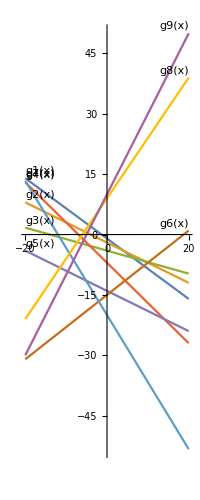

```mathematica
(* Define Boundary Functions *)
g1[x_,y_]:=-3x-4y;
g2[x_,y_]:=x+2y;
g3[x_,y_]:=-2x-7y;
g4[x_,y_]:=2x+2y;
g5[x_,y_]:=x+2y;
g6[x_,y_]:=-4x+5y;
g7[x_,y_]:=5x+3y;
g8[x_,y_]:=-3x+2y;
g9[x_,y_]:=-2x+y;

b1=4;b2=-4;b3=28;b4=-14;b5=-28;b6=-75;b7=-60;b8=18;b9=10;

g1[x_]:=y/.Solve[g1[x,y]==b1,{y}][[1,1]]
g2[x_]:=y/.Solve[g2[x,y]==b2,{y}][[1,1]]
g3[x_]:=y/.Solve[g3[x,y]==b3,{y}][[1,1]]
g4[x_]:=y/.Solve[g4[x,y]==b4,{y}][[1,1]]
g5[x_]:=y/.Solve[g5[x,y]==b5,{y}][[1,1]]
g6[x_]:=y/.Solve[g6[x,y]==b6,{y}][[1,1]]
g7[x_]:=y/.Solve[g7[x,y]==b7,{y}][[1,1]]
g8[x_]:=y/.Solve[g8[x,y]==b8,{y}][[1,1]]
g9[x_]:=y/.Solve[g9[x,y]==b9,{y}][[1,1]]

Plot[{g1[x],g2[x],g3[x],g4[x],g5[x],g6[x],g7[x],g8[x],g9[x]},{x,-20,20},{AspectRatio->Automatic},PlotLabels->Placed[Automatic,Above]]
```

```mathematica
(* Defining all constraints with ≤ *)
(*  3x + 4y ≤ -04 *)
(*   x + 2y ≤ -04 *)
(*  2x + 7y ≤ -28 *)
(*  2x + 2y ≤ -14 *)
(* - x - 2y ≤  28 *)
(*  4x - 5y ≤  75 *)
(* -5x - 3y ≤  60 *)
(* -3x + 2y ≤  18 *)
(* -2x +  y ≤  10 *)

(* Adding in and solving for slack variables *)
(* s1 = -04 - 3x - 4y *)
(* s2 = -04 - 1x - 2y *)
(* s3 = -28 - 2x - 7y *)
(* s4 = -14 - 2x - 2y *)
(* s5 =  28 + 1x + 2y *)
(* s6 =  75 - 4x + 5y *)
(* s7 =  60 + 5x + 3y *)
(* s8 =  18 + 3x - 2y *)
(* s9 =  10 + 2x - 1y *)

(* Substituting x1= v1-v2,x2=v2-v4 into tableau*)
(* Objective function becomes: 10v1 - 10v2 + 6v3 - 6v4 - 12 *)

(* Create vector of variables for Bland's Rule *)
blandVec = {v1,v2,v3,v4,s1,s2,s3,s4,s5,s6,s7,s8,s9}

(* Defining t0 *)
m0={v1,v2,v3,v4,1,""};
m1 ={-3,3,-4,4,-04,s1};
m2 ={-1,1,-2,2,-04,s2};
m3 ={-2,2,-7,7,-28,s3};
m4 ={-2,2,-2,2,-14,s4};
m5 ={ 1,-1,2,-2,28,s5};
m6 ={-4,4,5,-5,75,s6};
m7 ={5,-5,3,-3,60,s7};
m8 ={3,-3,-2,2,18,s8};
m9 ={2,-2,-1,1,10,s9};
mobj={10,-10,6,-6,-12,z->min};
t0={m0,m1,m2,m3,m4,m5,m6,m7,m8,m9,mobj};
Print["t0 = ",MatrixForm[t0]]
```

{v1,v2,v3,v4,s1,s2,s3,s4,s5,s6,s7,s8,s9}

t0 = (v1 | v2 | v3 | v4 | 1 | 
-3 | 3 | -4 | 4 | -4 | s1
-1 | 1 | -2 | 2 | -4 | s2
-2 | 2 | -7 | 7 | -28 | s3
-2 | 2 | -2 | 2 | -14 | s4
1 | -1 | 2 | -2 | 28 | s5
-4 | 4 | 5 | -5 | 75 | s6
5 | -5 | 3 | -3 | 60 | s7
3 | -3 | -2 | 2 | 18 | s8
2 | -2 | -1 | 1 | 10 | s9
10 | -10 | 6 | -6 | -12 | z→min)

```mathematica
(* i0 = 2, since it's first row, no need to use max test *)
(* jStar is possibly 2 or 4, but bland's rule breaks the tie for 2 *)
(* iStar = 2 *)
(* jStar = 2 *)

t1 = pivot[t0,2,2];
Print["t1 = ",MatrixForm[t1]]
```

t1 = (v1 | s1 | v3 | v4 | 1 | 
1 | 1/3 | 4/3 | -4/3 | 4/3 | v2
0 | 1/3 | -2/3 | 2/3 | -8/3 | s2
0 | 2/3 | -13/3 | 13/3 | -76/3 | s3
0 | 2/3 | 2/3 | -2/3 | -34/3 | s4
0 | -1/3 | 2/3 | -2/3 | 80/3 | s5
0 | 4/3 | 31/3 | -31/3 | 241/3 | s6
0 | -5/3 | -11/3 | 11/3 | 160/3 | s7
0 | -1 | -6 | 6 | 14 | s8
0 | -2/3 | -11/3 | 11/3 | 22/3 | s9
0 | -10/3 | -22/3 | 22/3 | -76/3 | z→min)

```mathematica
(* i0 = 3 *)
(* jStar can be 2 or 4. Bland's rule says v4 before s2. *)
(* jStar = 4 *)
(* iStar = 3 by max test*)
iStarCandidatesT2={(-4/4),(2/-8)};
Print["Manual iStar Candidates: ", iStarCandidatesT2];

findStarsP1[t1,3,blandVec,True]
t2=pivot[t1,3,4];
Print["t2 = ",MatrixForm[t2]]
```

Manual iStar Candidates: {-1,-1/4}

Max Comparison Array: {1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-1,-1/4}
Max Position: {{2}}
Extraction: {{v2}}

basicVars: {{},{v2},{s2},{s3},{s4},{s5},{s6},{s7},{s8},{s9},{z→min}}
Non-Basic Vars: {v1,s1,v3,v4,1,}
jStar Candidates: {s1,v4}
jStar Bland's Rule Result: v4
jStar: 4
iStar Candidates: {v2}
iStar Bland's Rule Result: iStarBlandResult
iStar: 2

{2,4}

t2 = (v1 | s1 | v3 | s2 | 1 | 
1 | 1 | 0 | -2 | -4 | v2
0 | -1/2 | 1 | 3/2 | 4 | v4
0 | -3/2 | 0 | 13/2 | -8 | s3
0 | 1 | 0 | -1 | -14 | s4
0 | 0 | 0 | -1 | 24 | s5
0 | 13/2 | 0 | -31/2 | 39 | s6
0 | -7/2 | 0 | 11/2 | 68 | s7
0 | -4 | 0 | 9 | 38 | s8
0 | -5/2 | 0 | 11/2 | 22 | s9
0 | -7 | 0 | 11 | 4 | z→min)

```mathematica
findStarsP1[t2,2,blandVec,True]
t3=pivot[t2,2,1];
Print["t3 = ",MatrixForm[t3]]
```

Max Comparison Array: {1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-1/4}
Max Position: {{2}}
Extraction: {{v2}}

basicVars: {{},{v2},{v4},{s3},{s4},{s5},{s6},{s7},{s8},{s9},{z→min}}
Non-Basic Vars: {v1,s1,v3,s2,1,}
jStar Candidates: {v1,s1}
jStar Bland's Rule Result: v1
jStar: 1
iStar Candidates: {v2}
iStar Bland's Rule Result: iStarBlandResult
iStar: 2

{2,1}

t3 = (v2 | s1 | v3 | s2 | 1 | 
1 | -1 | 0 | 2 | 4 | v1
0 | -1/2 | 1 | 3/2 | 4 | v4
0 | -3/2 | 0 | 13/2 | -8 | s3
0 | 1 | 0 | -1 | -14 | s4
0 | 0 | 0 | -1 | 24 | s5
0 | 13/2 | 0 | -31/2 | 39 | s6
0 | -7/2 | 0 | 11/2 | 68 | s7
0 | -4 | 0 | 9 | 38 | s8
0 | -5/2 | 0 | 11/2 | 22 | s9
0 | -7 | 0 | 11 | 4 | z→min)

```mathematica
findStarsP1[t3,4,blandVec,True]
t4=pivot[t3,4,4];
Print["t4 = ",MatrixForm[t4]//N]
```

Max Comparison Array: {1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-13/16}
Max Position: {{4}}
Extraction: {{s3}}

basicVars: {{},{v1},{v4},{s3},{s4},{s5},{s6},{s7},{s8},{s9},{z→min}}
Non-Basic Vars: {v2,s1,v3,s2,1,}
jStar Candidates: {s2}
jStar Bland's Rule Result: v1
jStar: 4
iStar Candidates: {s3}
iStar Bland's Rule Result: iStarBlandResult
iStar: 4

{4,4}

t4 = (v2 | s1 | v3 | s3 | 1. | 
1. | -0.538462 | 0. | 0.307692 | 6.46154 | v1
0. | -0.153846 | 1. | 0.230769 | 5.84615 | v4
0. | 0.230769 | 0. | 0.153846 | 1.23077 | s2
0. | 0.769231 | 0. | -0.153846 | -15.2308 | s4
0. | -0.230769 | 0. | -0.153846 | 22.7692 | s5
0. | 2.92308 | 0. | -2.38462 | 19.9231 | s6
0. | -2.23077 | 0. | 0.846154 | 74.7692 | s7
0. | -1.92308 | 0. | 1.38462 | 49.0769 | s8
0. | -1.23077 | 0. | 0.846154 | 28.7692 | s9
0. | -4.46154 | 0. | 1.69231 | 17.5385 | z→min)

```mathematica
findStarsP1[t4,5,blandVec,True]
t5=pivot[t4,3,2];
Print["t5 = ",MatrixForm[t5]//N]
```

Max Comparison Array: {1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-1/12,-1/38,1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-5/99}
Max Position: {{2}}
Extraction: {{v1}}

basicVars: {{},{v1},{v4},{s2},{s4},{s5},{s6},{s7},{s8},{s9},{z→min}}
Non-Basic Vars: {v2,s1,v3,s3,1,}
jStar Candidates: {s1}
jStar Bland's Rule Result: v1
jStar: 2
iStar Candidates: {v1}
iStar Bland's Rule Result: iStarBlandResult
iStar: 2

{2,2}

t5 = (v2 | v4 | v3 | s3 | 1. | 
1. | 3.5 | -3.5 | -0.5 | -14. | v1
0. | -6.5 | 6.5 | 1.5 | 38. | s1
0. | -1.5 | 1.5 | 0.5 | 10. | s2
0. | -5. | 5. | 1. | 14. | s4
0. | 1.5 | -1.5 | -0.5 | 14. | s5
0. | -19. | 19. | 2. | 131. | s6
0. | 14.5 | -14.5 | -2.5 | -10. | s7
0. | 12.5 | -12.5 | -1.5 | -24. | s8
0. | 8. | -8. | -1. | -18. | s9
0. | 29. | -29. | -5. | -152. | z→min)

```mathematica
findStarsP1[t5,2,blandVec,True]
t6=pivot[t5,2,1];
Print["t6 = ",MatrixForm[t6]//N];
```

Max Comparison Array: {1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-1/14}
Max Position: {{2}}
Extraction: {{v1}}

basicVars: {{},{v1},{s1},{s2},{s4},{s5},{s6},{s7},{s8},{s9},{z→min}}
Non-Basic Vars: {v2,v4,v3,s3,1,}
jStar Candidates: {v2,v4}
jStar Bland's Rule Result: v2
jStar: 1
iStar Candidates: {v1}
iStar Bland's Rule Result: iStarBlandResult
iStar: 2

{2,1}

t6 = (v1 | v4 | v3 | s3 | 1. | 
1. | -3.5 | 3.5 | 0.5 | 14. | v2
0. | -6.5 | 6.5 | 1.5 | 38. | s1
0. | -1.5 | 1.5 | 0.5 | 10. | s2
0. | -5. | 5. | 1. | 14. | s4
0. | 1.5 | -1.5 | -0.5 | 14. | s5
0. | -19. | 19. | 2. | 131. | s6
0. | 14.5 | -14.5 | -2.5 | -10. | s7
0. | 12.5 | -12.5 | -1.5 | -24. | s8
0. | 8. | -8. | -1. | -18. | s9
0. | 29. | -29. | -5. | -152. | z→min)

```mathematica
findStarsP1[t6,8,blandVec,True]
t7=pivot[t6,7,2];
Print["t7 = ",MatrixForm[t7]//N]
```

Max Comparison Array: {1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-1/4,-13/76,-3/20,-5/14,1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-19/131,-29/20}
Max Position: {{8}}
Extraction: {{s7}}

basicVars: {{},{v2},{s1},{s2},{s4},{s5},{s6},{s7},{s8},{s9},{z→min}}
Non-Basic Vars: {v1,v4,v3,s3,1,}
jStar Candidates: {v4}
jStar Bland's Rule Result: v2
jStar: 2
iStar Candidates: {s7}
iStar Bland's Rule Result: iStarBlandResult
iStar: 8

{8,2}

t7 = (v1 | s6 | v3 | s3 | 1. | 
1. | 0.184211 | 0. | 0.131579 | -10.1316 | v2
0. | 0.342105 | 0. | 0.815789 | -6.81579 | s1
0. | 0.0789474 | 0. | 0.342105 | -0.342105 | s2
0. | 0.263158 | 0. | 0.473684 | -20.4737 | s4
0. | -0.0789474 | 0. | -0.342105 | 24.3421 | s5
0. | -0.0526316 | 1. | 0.105263 | 6.89474 | v4
0. | -0.763158 | 0. | -0.973684 | 89.9737 | s7
0. | -0.657895 | 0. | -0.184211 | 62.1842 | s8
0. | -0.421053 | 0. | -0.157895 | 37.1579 | s9
0. | -1.52632 | 0. | -1.94737 | 47.9474 | z→min)

```mathematica
findStarsP1[t7,2,blandVec,True]
t8=pivot[t7,2,1];
Print["t8 = ",MatrixForm[t8]//N]
```

Max Comparison Array: {1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-38/385}
Max Position: {{2}}
Extraction: {{v2}}

basicVars: {{},{v2},{s1},{s2},{s4},{s5},{v4},{s7},{s8},{s9},{z→min}}
Non-Basic Vars: {v1,s6,v3,s3,1,}
jStar Candidates: {v1,s6,s3}
jStar Bland's Rule Result: v1
jStar: 1
iStar Candidates: {v2}
iStar Bland's Rule Result: iStarBlandResult
iStar: 2

{2,1}

t8 = (v2 | s6 | v3 | s3 | 1. | 
1. | -0.184211 | 0. | -0.131579 | 10.1316 | v1
0. | 0.342105 | 0. | 0.815789 | -6.81579 | s1
0. | 0.0789474 | 0. | 0.342105 | -0.342105 | s2
0. | 0.263158 | 0. | 0.473684 | -20.4737 | s4
0. | -0.0789474 | 0. | -0.342105 | 24.3421 | s5
0. | -0.0526316 | 1. | 0.105263 | 6.89474 | v4
0. | -0.763158 | 0. | -0.973684 | 89.9737 | s7
0. | -0.657895 | 0. | -0.184211 | 62.1842 | s8
0. | -0.421053 | 0. | -0.157895 | 37.1579 | s9
0. | -1.52632 | 0. | -1.94737 | 47.9474 | z→min)

```mathematica
findStarsP1[t8,3,blandVec,True]
t9=pivot[t8,2,4];
Print["t9 = ",MatrixForm[t9]//N]
```

Max Comparison Array: {1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-1/77,-31/259}
Max Position: {{3}}
Extraction: {{s1}}

basicVars: {{},{v1},{s1},{s2},{s4},{s5},{v4},{s7},{s8},{s9},{z→min}}
Non-Basic Vars: {v2,s6,v3,s3,1,}
jStar Candidates: {s6,s3}
jStar Bland's Rule Result: s3
jStar: 4
iStar Candidates: {s1}
iStar Bland's Rule Result: iStarBlandResult
iStar: 3

{3,4}

t9 = (v2 | s6 | v3 | v1 | 1. | 
7.6 | -1.4 | 0. | -7.6 | 77. | s3
6.2 | -0.8 | 0. | -6.2 | 56. | s1
2.6 | -0.4 | 0. | -2.6 | 26. | s2
3.6 | -0.4 | 0. | -3.6 | 16. | s4
-2.6 | 0.4 | 0. | 2.6 | -2. | s5
0.8 | -0.2 | 1. | -0.8 | 15. | v4
-7.4 | 0.6 | 0. | 7.4 | 15. | s7
-1.4 | -0.4 | 0. | 1.4 | 48. | s8
-1.2 | -0.2 | 0. | 1.2 | 25. | s9
-14.8 | 1.2 | 0. | 14.8 | -102. | z→min)

```mathematica
findStarsP1[t9,6,blandVec,True]
t10=pivot[t9,2,4];
Print["t10 = ",MatrixForm[t10]//N]
```

Max Comparison Array: {1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-38/385,-31/280,-1/10,-9/40,-13/10}
Max Position: {{6}}
Extraction: {{s5}}

basicVars: {{},{s3},{s1},{s2},{s4},{s5},{v4},{s7},{s8},{s9},{z→min}}
Non-Basic Vars: {v2,s6,v3,v1,1,}
jStar Candidates: {s6,v1}
jStar Bland's Rule Result: v1
jStar: 4
iStar Candidates: {s5}
iStar Bland's Rule Result: iStarBlandResult
iStar: 6

{6,4}

t10 = (v2 | s6 | v3 | s3 | 1. | 
1. | -0.184211 | 0. | -0.131579 | 10.1316 | v1
0. | 0.342105 | 0. | 0.815789 | -6.81579 | s1
0. | 0.0789474 | 0. | 0.342105 | -0.342105 | s2
0. | 0.263158 | 0. | 0.473684 | -20.4737 | s4
0. | -0.0789474 | 0. | -0.342105 | 24.3421 | s5
0. | -0.0526316 | 1. | 0.105263 | 6.89474 | v4
0. | -0.763158 | 0. | -0.973684 | 89.9737 | s7
0. | -0.657895 | 0. | -0.184211 | 62.1842 | s8
0. | -0.421053 | 0. | -0.157895 | 37.1579 | s9
0. | -1.52632 | 0. | -1.94737 | 47.9474 | z→min)

```mathematica
t10==t8
```

True

```mathematica
minSol=Map[MatrixForm,runSimplex[t0,blandVec,100,True]];
```

Max Comparison Array: {1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-3/4}
Max Position: {{2}}
Extraction: {{s1}}

basicVars: {{},{s1},{s2},{s3},{s4},{s5},{s6},{s7},{s8},{s9},{z→min}}
Non-Basic Vars: {v1,v2,v3,v4,1,}
jStar Candidates: {v2,v4}
jStar Bland's Rule Result: v2
jStar: 2
iStar Candidates: {s1}
iStar Bland's Rule Result: iStarBlandResult
iStar: 2

Max Comparison Array: {1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-1,-1/4}
Max Position: {{2}}
Extraction: {{v2}}

basicVars: {{},{v2},{s2},{s3},{s4},{s5},{s6},{s7},{s8},{s9},{z→min}}
Non-Basic Vars: {v1,s1,v3,v4,1,}
jStar Candidates: {s1,v4}
jStar Bland's Rule Result: v4
jStar: 4
iStar Candidates: {v2}
iStar Bland's Rule Result: iStarBlandResult
iStar: 2

Max Comparison Array: {1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-1/4}
Max Position: {{3}}
Extraction: {{s2}}

basicVars: {{},{v4},{s2},{s3},{s4},{s5},{s6},{s7},{s8},{s9},{z→min}}
Non-Basic Vars: {v1,s1,v3,v2,1,}
jStar Candidates: {v1,s1}
jStar Bland's Rule Result: v1
jStar: 1
iStar Candidates: {s2}
iStar Bland's Rule Result: iStarBlandResult
iStar: 3

Max Comparison Array: {1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-13/16}
Max Position: {{4}}
Extraction: {{s3}}

basicVars: {{},{v4},{v1},{s3},{s4},{s5},{s6},{s7},{s8},{s9},{z→min}}
Non-Basic Vars: {s2,s1,v3,v2,1,}
jStar Candidates: {s2}
jStar Bland's Rule Result: v1
jStar: 1
iStar Candidates: {s3}
iStar Bland's Rule Result: iStarBlandResult
iStar: 4

Max Comparison Array: {1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-1/38,-1/12,1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-5/99}
Max Position: {{3}}
Extraction: {{v1}}

basicVars: {{},{v4},{v1},{s2},{s4},{s5},{s6},{s7},{s8},{s9},{z→min}}
Non-Basic Vars: {s3,s1,v3,v2,1,}
jStar Candidates: {s1}
jStar Bland's Rule Result: v1
jStar: 2
iStar Candidates: {v1}
iStar Bland's Rule Result: iStarBlandResult
iStar: 3

Max Comparison Array: {1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-1/14,1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-5/21}
Max Position: {{5}}
Extraction: {{s4}}

basicVars: {{},{v4},{s1},{s2},{s4},{s5},{s6},{s7},{s8},{s9},{z→min}}
Non-Basic Vars: {s3,v1,v3,v2,1,}
jStar Candidates: {s3,v2}
jStar Bland's Rule Result: v2
jStar: 4
iStar Candidates: {s4}
iStar Bland's Rule Result: iStarBlandResult
iStar: 5

Max Comparison Array: {1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-1/14,1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-3/182,1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-29/306,-5/22,-4/11}
Max Position: {{10}}
Extraction: {{s9}}

basicVars: {{},{v4},{s1},{s2},{v2},{s5},{s6},{s7},{s8},{s9},{z→min}}
Non-Basic Vars: {s3,v1,v3,s4,1,}
jStar Candidates: {s4}
jStar Bland's Rule Result: v2
jStar: 4
iStar Candidates: {s9}
iStar Bland's Rule Result: iStarBlandResult
iStar: 10

Max Comparison Array: {1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,-5/278,-3/706,-11/362,1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609,3/22}
Max Position: {{8}}
Extraction: {{s7}}

basicVars: {{},{v4},{s1},{s2},{v2},{s5},{s6},{s7},{s8},{s4},{z→min}}
Non-Basic Vars: {s3,v1,v3,s9,1,}
jStar Candidates: {s3}
jStar Bland's Rule Result: v2
jStar: 1
iStar Candidates: {s7}
iStar Bland's Rule Result: iStarBlandResult
iStar: 8

Reached optimal Tableaux

```mathematica
mobjneg={-10,10,-6,6,12,-z->min};
t0neg={m0,m1,m2,m3,m4,m5,m6,m7,m8,m9,mobjneg};
maxSol=Map[MatrixForm,runSimplex[t0neg,blandVec,100,False]];
Print["Steps for Minimization: ", maxSol];
```

Reached optimal Tableaux

Steps for Minimization: {(v1 | v2 | v3 | v4 | 1 | 
-3 | 3 | -4 | 4 | -4 | s1
-1 | 1 | -2 | 2 | -4 | s2
-2 | 2 | -7 | 7 | -28 | s3
-2 | 2 | -2 | 2 | -14 | s4
1 | -1 | 2 | -2 | 28 | s5
-4 | 4 | 5 | -5 | 75 | s6
5 | -5 | 3 | -3 | 60 | s7
3 | -3 | -2 | 2 | 18 | s8
2 | -2 | -1 | 1 | 10 | s9
-10 | 10 | -6 | 6 | 12 | -z→min),(v1 | s1 | v3 | v4 | 1 | 
1 | 1/3 | 4/3 | -4/3 | 4/3 | v2
0 | 1/3 | -2/3 | 2/3 | -8/3 | s2
0 | 2/3 | -13/3 | 13/3 | -76/3 | s3
0 | 2/3 | 2/3 | -2/3 | -34/3 | s4
0 | -1/3 | 2/3 | -2/3 | 80/3 | s5
0 | 4/3 | 31/3 | -31/3 | 241/3 | s6
0 | -5/3 | -11/3 | 11/3 | 160/3 | s7
0 | -1 | -6 | 6 | 14 | s8
0 | -2/3 | -11/3 | 11/3 | 22/3 | s9
0 | 10/3 | 22/3 | -22/3 | 76/3 | -z→min),(v1 | s1 | v3 | v2 | 1 | 
3/4 | 1/4 | 1 | -3/4 | 1 | v4
1/2 | 1/2 | 0 | -1/2 | -2 | s2
13/4 | 7/4 | 0 | -13/4 | -21 | s3
-1/2 | 1/2 | 0 | 1/2 | -12 | s4
-1/2 | -1/2 | 0 | 1/2 | 26 | s5
-31/4 | -5/4 | 0 | 31/4 | 70 | s6
11/4 | -3/4 | 0 | -11/4 | 57 | s7
9/2 | 1/2 | 0 | -9/2 | 20 | s8
11/4 | 1/4 | 0 | -11/4 | 11 | s9
-11/2 | 3/2 | 0 | 11/2 | 18 | -z→min),(s2 | s1 | v3 | v2 | 1 | 
3/2 | -1/2 | 1 | 0 | 4 | v4
2 | -1 | 0 | 1 | 4 | v1
13/2 | -3/2 | 0 | 0 | -8 | s3
-1 | 1 | 0 | 0 | -14 | s4
-1 | 0 | 0 | 0 | 24 | s5
-31/2 | 13/2 | 0 | 0 | 39 | s6
11/2 | -7/2 | 0 | 0 | 68 | s7
9 | -4 | 0 | 0 | 38 | s8
11/2 | -5/2 | 0 | 0 | 22 | s9
-11 | 7 | 0 | 0 | -4 | -z→min),(s3 | s1 | v3 | v2 | 1 | 
3/13 | -2/13 | 1 | 0 | 76/13 | v4
4/13 | -7/13 | 0 | 1 | 84/13 | v1
2/13 | 3/13 | 0 | 0 | 16/13 | s2
-2/13 | 10/13 | 0 | 0 | -198/13 | s4
-2/13 | -3/13 | 0 | 0 | 296/13 | s5
-31/13 | 38/13 | 0 | 0 | 259/13 | s6
11/13 | -29/13 | 0 | 0 | 972/13 | s7
18/13 | -25/13 | 0 | 0 | 638/13 | s8
11/13 | -16/13 | 0 | 0 | 374/13 | s9
-22/13 | 58/13 | 0 | 0 | -228/13 | -z→min),(s3 | v1 | v3 | v2 | 1 | 
1/7 | 2/7 | 1 | -2/7 | 4 | v4
4/7 | -13/7 | 0 | 13/7 | 12 | s1
2/7 | -3/7 | 0 | 3/7 | 4 | s2
2/7 | -10/7 | 0 | 10/7 | -6 | s4
-2/7 | 3/7 | 0 | -3/7 | 20 | s5
-5/7 | -38/7 | 0 | 38/7 | 55 | s6
-3/7 | 29/7 | 0 | -29/7 | 48 | s7
2/7 | 25/7 | 0 | -25/7 | 26 | s8
1/7 | 16/7 | 0 | -16/7 | 14 | s9
6/7 | -58/7 | 0 | 58/7 | 36 | -z→min),(s3 | v1 | v3 | s4 | 1 | 
1/5 | 0 | 1 | -1/5 | 14/5 | v4
1/5 | 0 | 0 | 13/10 | 99/5 | s1
1/5 | 0 | 0 | 3/10 | 29/5 | s2
-1/5 | 1 | 0 | 7/10 | 21/5 | v2
-1/5 | 0 | 0 | -3/10 | 91/5 | s5
-9/5 | 0 | 0 | 19/5 | 389/5 | s6
2/5 | 0 | 0 | -29/10 | 153/5 | s7
1 | 0 | 0 | -5/2 | 11 | s8
3/5 | 0 | 0 | -8/5 | 22/5 | s9
-4/5 | 0 | 0 | 29/5 | 354/5 | -z→min),(v2 | v1 | v3 | s4 | 1 | 
-1 | 1 | 1 | 1/2 | 7 | v4
-1 | 1 | 0 | 2 | 24 | s1
-1 | 1 | 0 | 1 | 10 | s2
-5 | 5 | 0 | 7/2 | 21 | s3
1 | -1 | 0 | -1 | 14 | s5
9 | -9 | 0 | -5/2 | 40 | s6
-2 | 2 | 0 | -3/2 | 39 | s7
-5 | 5 | 0 | 1 | 32 | s8
-3 | 3 | 0 | 1/2 | 17 | s9
4 | -4 | 0 | 3 | 54 | -z→min),(v2 | s6 | v3 | s4 | 1 | 
0 | -1/9 | 1 | 2/9 | 103/9 | v4
0 | -1/9 | 0 | 31/18 | 256/9 | s1
0 | -1/9 | 0 | 13/18 | 130/9 | s2
0 | -5/9 | 0 | 19/9 | 389/9 | s3
0 | 1/9 | 0 | -13/18 | 86/9 | s5
1 | -1/9 | 0 | -5/18 | 40/9 | v1
0 | -2/9 | 0 | -37/18 | 431/9 | s7
0 | -5/9 | 0 | -7/18 | 488/9 | s8
0 | -1/3 | 0 | -1/3 | 91/3 | s9
0 | 4/9 | 0 | 37/9 | 326/9 | -z→min)}